# Prime Sieves Project

In this project we will investigate prime sieves. The point of this project is to generate lists of primes smaller than a given number n, and do it in the shortest possible time. The two sieves that we will be studying today will be the Sieve of Eratosthenes and Sieve of Sundaram.

After the implementation of each algorithm we will time them for different values of n, and compare them against each other and decide which one is the faster one.

## Sieve of Eratosthenes

The first sieve we will implement is the sieve of Eratosthenes. The concept behind this sieve is that for each number we encounter starting from 2, we will remove all the numbers all the way to n, that are divisible by 2. Then we will do the same thing for 3, 5 and so on and so forth. 
What is left will be a list of primes. 

The number of times we will repeat this process will be equal to the square root of n. Since by this point we would have checked all the numbers. 
Below is a mathematical implementation of this sieve:

```mathematica
eratosthenes2[n0_]:=Module[{n=n0},
(*create a list from 1 to n*)
list=Range[1, n];
(*remove one from the list*)
list=Delete[list,1];
(*find the square root*)
n2 = Floor[Sqrt[n]];
(*go from 1 to the square root of n*)
For[i=1,i≤n2, i++,
(*find the first prime in the list*)
c=list[[1]];
(*remove all the elements that are divisible by that prime*)
list=Select[list, Mod[#,i+1]≠0&];
(*add this element back to the list since it was removed*)
list=AppendTo[list,c];
]
Sort[DeleteDuplicates[list]];
(*sort the list and delete any duplicates, this happens for some values of c*)
list2 =Sort[DeleteDuplicates[list]];
(*return the list of primes*)
list2
]
```

Now let’s see if our function works for a couple of values:

```mathematica
eratosthenes2[10]
eratosthenes2[100]
eratosthenes2[200]
```

{2,3,5,7}

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199}

As we see it works pretty well so now let’s build a timing function that we will be using later. 
This function will find calculate how much time it takes to calculate 2^n.

```mathematica
t1[n_]:=Timing[eratosthenes2[2^n]][[1]];
```

Let’s now try if this function works:

```mathematica
t1[5]
t1[10]
t1[15]
```

0.00027

0.009933

0.80775

This works really well so now we can go on to build the sieve of Sunduram and in the end we will compare their run times.

## Sieve of Sunduram

This sieve accomplishes almost the same thing as the sieve of Eratosthenes. It gives us all the odd primes up to 2n+1 where n is the input. 

Sieve of Sunduram will will remove all the numbers with indexes i + j + 2 i j, where i and j are  This will remove all the composite numbers and everything that is left will be multiplied by 2 and added 1. And this will give us all the odd prime numbers. 

Below there is the mathematical implementation.

```mathematica
sunduram[n0_]:=Module[{n=n0},
(*create a list from 1 to n*)
l1 = Range[1,n]; 
(*create an empty list to store all the elements that were removed*)
l2={};

(*let i go from 1 to j*)
For[i=1,i≤j,i++,
(*let j=i, and go until i+j+2*i*j≤n*)
For[j=i,i+j+2*i*j≤n,j++, 
(*add to the l2 all elements that were removed*)
AppendTo[l2,l1[[i+j+2*i*j]]];
]
];
(*find all the elements of l1 that are not in l2*)
l1 = Complement[l1,l2];
(*multiply all elements of a list by 2 and add 1*)
l1 = l1*2+1;
(*return the list*)
l1];
```

Now let’s try and see if our function works:

```mathematica
sunduram[10]
sunduram[200]
```

{3,5,7,9,11,13,15,17,19,21}

{3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199,201,203,205,207,209,211,213,215,217,219,221,223,225,227,229,231,233,235,237,239,241,243,245,247,249,251,253,255,257,259,261,263,265,267,269,271,273,275,277,279,281,283,285,287,289,291,293,295,297,299,301,303,305,307,309,311,313,315,317,319,321,323,325,327,329,331,333,335,337,339,341,343,345,347,349,351,353,355,357,359,361,363,365,367,369,371,373,375,377,379,381,383,385,387,389,391,393,395,397,399,401}

This seems to be working well. Now let’s build a timing function that we will need when comparing the two algorithms. 

This function takes a number n, and calculates how much time it takes to generate numbers up to 2^n.

```mathematica
t2[n_]:=Timing[sunduram[2^n]][[1]];
```

Now let’s try and see if this works.

```mathematica
t2[5]
t2[10]
t2[14]
```

0.000075

0.000125

0.002885

Function seems to be running alright. And now we can go ahead with the comparison of the running times.

## Comparing the running times

Now let’s go ahead and try to compare those two algorithms together. We have two timing algorithms and now all we need to do is to see how the times compare. 

Let’s first plot the how much it takes for the sieve of Eratosthenes for 2^5all the way to 2^15.

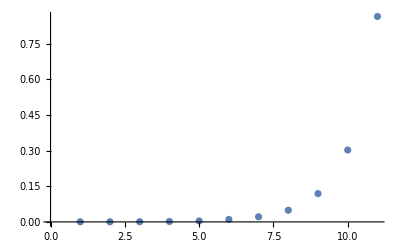

```mathematica
(*list of n*)
mylist=Range[5,15];
timingEratosthenes = Map[t1,mylist];
ListPlot[timingEratosthenes]
```

Now let’s do the same thing for the sieve of Sunduram

```mathematica
timingSunduram= Map[t2,mylist];
```

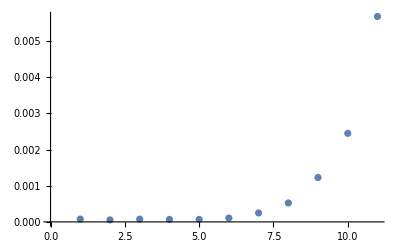

```mathematica
ListPlot[timingSunduram]
```

This seems to be faster but let’s graph them together and see the difference.

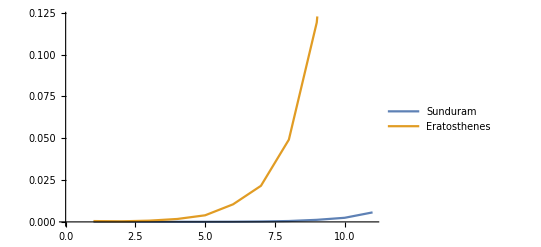

```mathematica
ListLinePlot[{timingSunduram,timingEratosthenes},PlotLegends->{"Sunduram","Eratosthenes"}]
```

This clearly shows that my implementation of the sieve of Sunduram  is faster than the sieve of Eratosthenes. So from my implementation I would say with proof that the sieve of Eratosthenes is faster than the sieve of Sunduram. 

Here are the actual values that we got for each:

```mathematica
timingSunduram
timingEratosthenes
```

{0.000078,0.000055,0.000077,0.000069,0.000068,0.000107,0.000248,0.000524,0.001226,0.002449,0.005679}

{0.0005,0.000342,0.000744,0.001744,0.003947,0.0105,0.021572,0.049152,0.119157,0.302763,0.86526}

And just for fun I will use the sieve of Sunduram to calculate primes for n being 1 million.

```mathematica
Timing[sunduram[1000000]][[1]]
```

0.158766

And that only took 0.15 seconds faster so I would say it is pretty fast.